# Estimating a Population Proportion

## Jie Frye Wolfram Summer School 2017

## Learning Objectives

Construct a confidence interval to estimate a population proportion.

Interpret the confidence interval in context.

Use code to visualize and calculate confidence intervals.

## Overview

#### Inferential statistics

Limited sample of data

Want to know something about the population that this sample comes from.

#### Example

Sample: 1000 U.S. college students are surveyed for their genders.

Want to know: true population proportion of female college students.

#### Certainty

Estimate: In 2010, females make up 57% of the U.S. college population.

How certain are we?

## Behavior of Sample Proportions

We use a simulation to collect numerous samples to study the center, spread, and shape of the distribution of sample proportions. Our goal is to create a probability model that describes the long-run behavior of proportions from random samples.

Create a variable containing 10000 values, 4300 of them are 0 and 5700 of them are 1. You have just created a population of 10000 individuals, 57% of whom are female.

```mathematica
dist=Flatten[{Table[0,{i,4300}],Table[1,{i,5700}]}];
PieChart[{Total[dist],Length[dist]-Total[dist]}]
```

-Graphics-

Take a random sample of 200 points from this population and calculate the sample proportion. Is that a reasonable result?

```mathematica
RandomSample[dist,200];
Mean[%]//N
```

0.565

Extend your work to create code that will take samples of size n = 200, 400 times, and store the sample proportions p̂ in a vector.

```mathematica
sample=Table[Mean[RandomSample[dist,200]],{i,400}];
Table[PieChart[{Part[sample,i],1-Part[sample,i]}],{i,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

What is the distribution of p̂?

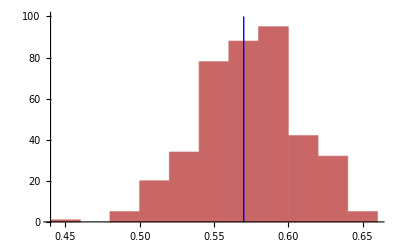

```mathematica
Show[Histogram[sample],ContourPlot[{x==.57},{x,.56,.58},{y,0,100},ContourStyle->Blue,ColorFunction->Automatic,Frame->False,Axes->True]]
```

## Distribution of Sample Proportions

Based on our intuition and what we observed with the applet, we might expect the following about the distribution of sample proportions that come from a population where p = 0.57:

Center: the mean of the distribution of sample proportions should be p.

μ_(p̂)=p

Spread: for large sample size, we expect sample proportions of females not to stray too far from the population proportion 0.57. Sample proportions that are very low or very high will be unusual.

σ_(p̂)=√((p(1-p))/n)

Shape: the shape of the distribution of sample proportions may be somewhat bell-shaped.

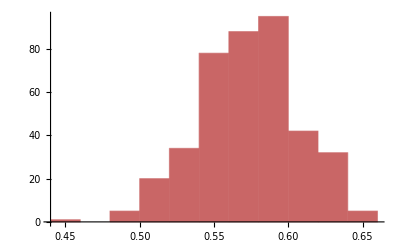
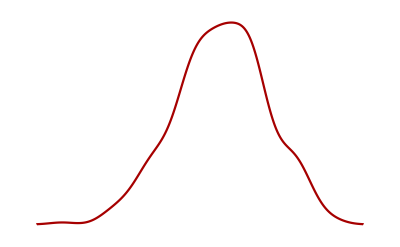

```mathematica
Overlay[{Histogram[sample],SmoothHistogram[sample,Axes->False]}]
```

## Confidence Intervals

When our goal is to estimate p, we select a random sample from the population and use the p̂ as an estimate.

Since random samples vary, we state the amount of error that may be present.

Because sample proportions vary in a predictable way, we can make a probability statement about how confident we are in the process we used to estimate p.

Formula of confidence interval for estimating population proportion:

p̂±z·√((p̂(1-p̂))/n)

The critical value z is associated with interesting central areas under the standard normal curve.

```mathematica
f[x_]:=Table[PDF[NormalDistribution[0,σ],x],{σ,{1}}];
g[s_]:=PDF[NormalDistribution[0,1],s];
Manipulate[
Show[ Plot[f[x]//Evaluate,{x,-3,3}],Plot[f[x]//Evaluate,{x,-3,0.00001-InverseCDF[NormalDistribution[0,1],n]},Filling->Axis],Plot[f[x]//Evaluate,{x,3,InverseCDF[NormalDistribution[0,1],n]},Filling->Axis],
Graphics[
{
Line[{{InverseCDF[NormalDistribution[0,1],n],0},{InverseCDF[NormalDistribution[0,1],n],g[InverseCDF[NormalDistribution[0,1],n]]}}],

Line[{{0.0001-InverseCDF[NormalDistribution[0,1],n],0},{0.001-InverseCDF[NormalDistribution[0,1],n],g[InverseCDF[NormalDistribution[0,1],n]]}}],
{Thickness[0.01],Line[{{InverseCDF[NormalDistribution[0,1],n],-0.001},{0.001-InverseCDF[NormalDistribution[0,1],n],0}}]},
Text[Style[Row[{Style["z",Italic]," = ",NumberForm[InverseCDF[NormalDistribution[0,1],n+(1-n)/2],4]}],FontSize->19],{-1.8,0.35}],
Text[Style[Row[{"unshaded area = ",NumberForm[n,2]}],FontSize->14],{-0.35,0.1525}]
}
],
ImageSize->500],
{{n,.90,"confidence level"},.70,.99,Appearance->"Labeled"},SaveDefinitions->True
]
```

## Example

In April and May of 2011, the Pew Research Center surveyed cell phone users about 
voice calls and text messaging. They surveyed a random sample of 1914 cell phone users. 75% of the sample use text messaging. What is the 95% confidence interval for the proportion of all cell phone users use text messaging?

```mathematica
<<HypothesisTesting`
n=1914; phat=.75; CL=.95; mean=phat; stddev=Sqrt[phat*(1-phat)/n];
NormalCI[mean,stddev,ConfidenceLevel->CL]
```

{0.730601,0.769399}

Impact of confidence level

```mathematica
Manipulate[
Show[NumberLinePlot[Interval[NormalCI[mean,stddev,ConfidenceLevel->CL]],PlotRange->{.72,.78}],Graphics[{PointSize[Large],Blue,Point[{0.75,1}]}]],
{{CL,.95,"Confidence Level"},.7,.99,Appearance->"Labeled"}]
```

## What Does 95% Confident Really Mean?

“We are 95% confident that the interval from 0.73 and 0.77 actually does contain the true 
value of the population proportion p.”

This means that if we were to select many different samples of size 1914 and construct the 
corresponding confidence intervals, 95% of them would contain the true value of the population proportion p.

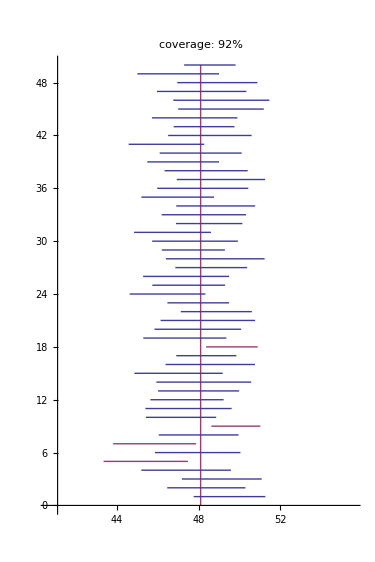

## Rules of Thumb

A normal model is a good fit if the expected number of successes and failures is at least 10. We can translate these conditions into formulas:

np≥10    and    n(1-p)≥10

## References

E. Hou and E. Madhekar, “Critical Value z* for z-Scores for Confidence Levels”. http://demonstrations.wolfram.com/CriticalValueZForZScoresForConfidenceLevels/